# The Quest of the outlier

```mathematica
labeledYes = Table[reducedOxyYes80[[i,1]]-> ToString@i,{i,30}];
labeledNo = Table[reducedOxyNo80[[i,1]]->ToString@i,{i,30}];
```

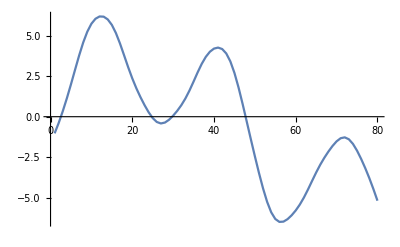

```mathematica
ListLinePlot[labeledNo[[1]],PlotLegends->Automatic]
```

```mathematica
labeledClusterYes = FindClusters[labeledYes,Method->"MeanShift"]//Column
```

{1,3,4,6,8,9,10,11,12,16,19,20,22,24,26,28,29}
{2,5,14,27}
{7,30}
{13,25}
{15,17,18,21,23}

```mathematica
check = FindClusters[reducedOxyYes80[[All,1]],Method->"MeanShift"];
```

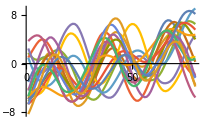
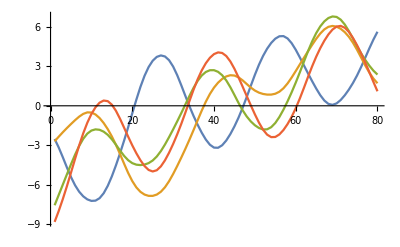
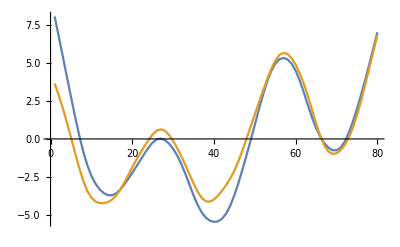
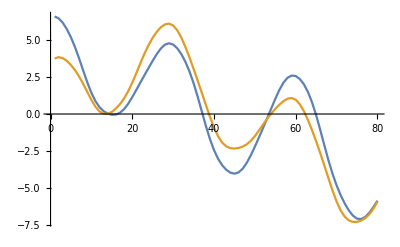
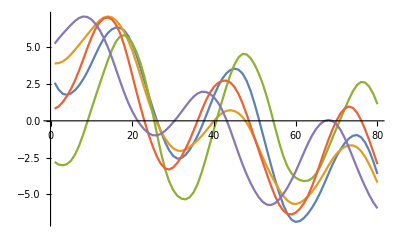

```mathematica
ListLinePlot/@check
```

```mathematica
labeledClusterNo = FindClusters[labeledNo,Method->"MeanShift"]//Column
```

{1,2,4,5,11,13,14,15,16,17,19,20,21,23,24,27,30}
{3,7,9,12,22,29}
{6,8,10,18,25,26,28}

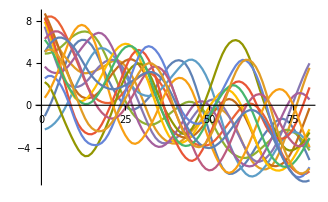
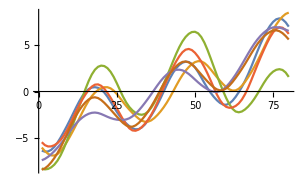
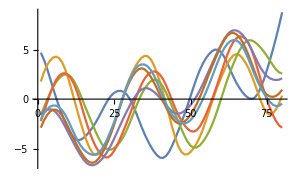

```mathematica
ListLinePlot/@FindClusters[reducedOxyNo80[[All,1]],Method->"MeanShift"]
```

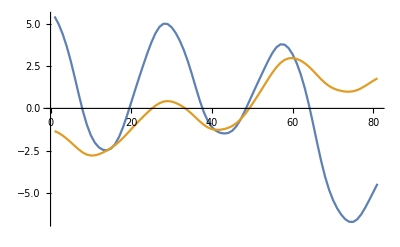

```mathematica
ListLinePlot[reducedPhasedOxyYes80[[18,All]]]
```

# Quest on the phased dataset

```mathematica
oxyPhasedYesMatlab = Import["/Users/ettoremariotti/Desktop/Semmestre/BCI/Project/BCI-ThoughtRecognition/data_students/segnali_belli/NIRSoxy_yesFasato.mat"];
numSamplesPhasedOxyYes = Dimensions[oxyPhasedYesMatlab][[3]];
phasedOxyYesRaw =  Table[Transpose[oxyPhasedYesMatlab[[1,1,x]]],{x,numSamplesPhasedOxyYes}];
```

```mathematica
oxyPhasedNoMatlab = Import["/Users/ettoremariotti/Desktop/Semmestre/BCI/Project/BCI-ThoughtRecognition/data_students/segnali_belli/NIRSoxy_noFasato.mat"];
numSamplesPhasedOxyNo = Dimensions[oxyPhasedNoMatlab][[3]];
phasedOxyNoRaw =  Table[Transpose[oxyPhasedNoMatlab[[1,1,x]]],{x,numSamplesPhasedOxyNo}];
```

```mathematica
phasedOxyYesRaw80={};
If[Dimensions[phasedOxyNoRaw[[#]]][[2]]==81,AppendTo[phasedOxyYesRaw80,Transpose@Drop[Transpose@phasedOxyYesRaw[[#]],-1]], AppendTo[phasedOxyYesRaw80,phasedOxyYesRaw[[#]]]]&/@Range[numSamplesPhasedOxyYes];

phasedOxyNoRaw80={};
If[Dimensions[phasedOxyNoRaw[[#]]][[2]]==81,AppendTo[phasedOxyNoRaw80,Transpose@Drop[Transpose@phasedOxyNoRaw[[#]],-1]], AppendTo[phasedOxyNoRaw80,phasedOxyNoRaw[[#]]]]&/@Range[numSamplesPhasedOxyNo];
```

```mathematica
reducedPhasedOxyNo80 = Transpose[DimensionReduce[Transpose@#,2,Method->"PrincipalComponentsAnalysis"]]&/@phasedOxyNoRaw80;
reducedPhasedOxyYes80 = Transpose[DimensionReduce[Transpose@#,2,Method->"PrincipalComponentsAnalysis"]]&/@phasedOxyYesRaw80;
```

```mathematica
labeledPhasedYes = Table[reducedPhasedOxyYes80[[i,1]]-> ToString@i,{i,30}];
labeledPhasedNo = Table[reducedPhasedOxyNo80[[i,1]]->ToString@i,{i,30}];
```

```mathematica
labeledPhasedClusterYes = FindClusters[labeledPhasedNo,Method->"MeanShift"]//Column
```

{1,14,27}
{2,11,13}
{3,6,7,8,10,12,17,18,19,20,22,25,26,28,29}
{4,5}
{9}
{15,16,21,23,24,30}

```mathematica
check = FindClusters[reducedPhasedOxyYes80[[All,1]],Method->"MeanShift"];
```

FindClusters::nosup: FindClusters does not support this type of data.

```mathematica
1994+18
```

2012